```mathematica
solarElectronNumberDensityData=Import["桌面/GitHub/neon/solar_e_density.dat"][[6;;1768]];
```

```mathematica
solarElectronNumberDensity=Interpolation[solarElectronNumberDensityData];
```

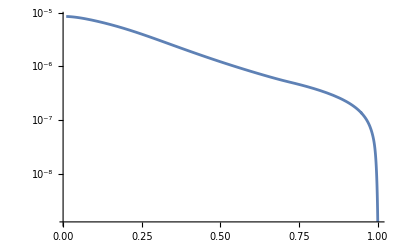

```mathematica
LogPlot[E^solarElectronNumberDensity[x]*NA*perVoltoMeVCubic,{x,10^-2,1}]
```

```mathematica
NA=6.02*10^23;(*Avogadro's number: mol^-1*)
GF=1.166*10^-23;(*Fermi constant: eV^-2*)
perVoltoElectronVoltCubic=(1.239*10^-4)^3;(*cm^-3 to eV^3*)
θ12=ArcSin[Sqrt[0.846]]/2;
Δm21=0.753*10^-4;
c=2.99*10^10;(*light speed cm/s*)
Rsun=6.963*10^5;(*solar radius km*)
dimCorrection=2.99*10^10*6.528*10^-22/(6.963*10^10);(*convert c/R_sun into MeV*)
```

```mathematica
HamiltonianFlavor[energy_,θ_,Δm2_]:=({{-Cos[2θ], Sin[2θ]}, {Sin[2θ], Cos[2θ]}})*Δm2/(4*energy*10^6 (*convert to eV*));
ne[x_]:=Sqrt[2]*GF*E^solarElectronNumberDensity[x]*NA*perVoltoElectronVoltCubic;
```

```mathematica
equations[energy_,θ_:θ12,Δm2_:Δm21]:=HamiltonianFlavor[energy,θ,Δm2].{ve[x],vμ[x]}
```

```mathematica
nuEnergy=3.54;
eqs=equations[nuEnergy];
sol=NDSolve[{I ve'[x]==eqs[[1]]+ve[x]If[0.01<=x*1.973*10^-10/Rsun<=1,ne[x*1.973*10^-10/Rsun],0],I vμ'[x]==eqs[[2]],ve[5*10^13]==1,vμ[5*10^13]==0},{ve,vμ},{x,5*10^13,10^16}];
```

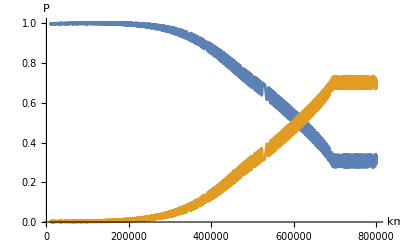

```mathematica
Plot[Evaluate[{ve[x/(1.973*10^-10)]*Conjugate[ve[x/(1.973*10^-10)]],vμ[x/(1.973*10^-10)]*Conjugate[vμ[x/(1.973*10^-10)]]}/.sol],{x,5*10^13*1.973*10^-10,800000},AxesLabel->{"km",P}]
```

```mathematica
Rsun/(1.973*10^-10)
```

3.52914×10^15

```mathematica
2/3.
```

0.666667

```mathematica
Re[Evaluate[{ve[x/(1.973*10^-10)]*Conjugate[ve[x/(1.973*10^-10)]]}/.sol[[1]]]]/.x->710000
```

{0.598582}

```mathematica
NIntegrate[{vμ[x/(1.973*10^-10)]*Conjugate[vμ[x/(1.973*10^-10)]]}/.sol[[1]],{x,700000,701000}]
```

{632.809}

```mathematica
%/1000
```

{0.632809}

```mathematica
%/1000
```

{0.375443}

```mathematica
0.632+0.375
```

1.007

```mathematica
1/3.
```

0.333333

```mathematica
UPMNS[L_,e_,θ12_:ArcSin[Sqrt[0.861]]/2,θ13_:ArcSin[Sqrt[0.1]]/2,θ23_:ArcSin[Sqrt[0.97]]/2,m12_:0.759*10^-4,m23_:23.2*10^-4,δ_:0]:={{Cos[θ12]Cos[θ13],Sin[θ12]Cos[θ13],Sin[θ13]Exp[-I δ]},
{-Sin[θ12]Cos[θ23]-Cos[θ12]Sin[θ13]Sin[θ23]Exp[I δ],Cos[θ12]Cos[θ23]-Sin[θ12]Sin[θ13]Sin[θ23]Exp[I δ],Cos[θ13]Sin[θ23]},
{Sin[θ12]Sin[θ23]-Cos[θ12]Sin[θ13]Cos[θ23]Exp[I δ],-Cos[θ12]Sin[θ23]-Sin[θ12]Sin[θ13]Cos[θ23]Exp[I δ],Cos[θ13]Cos[θ23]}}.{v1 Exp[2I*(1.27*m12)/e L],v2 ,v3  Exp[-2I*(1.27*m23)/e L]}
```

```mathematica
rho3[L_,e_]:=Expand[Simplify[Outer[Times,UPMNS[L,e],Transpose[Conjugate[UPMNS[0,e]]]],v1∈Reals&&v2∈Reals&&v3∈Reals]]/.{v1^2->1,v2^2->1,v3^2->1,v1 v3->0,v2 v3->0,v1 v2->0}
```

```mathematica
prob[L_,e_]:=rho3[L,e]*Conjugate[rho3[L,e]]
```

```mathematica
35000/10
```

3500

```mathematica
testprob=ParallelTable[prob[L,1],{L,0,35000,10}];
```

```mathematica
prob[0,1]//MatrixForm
```

(1.+0. ⅈ | 3.08149×10^-33+0. ⅈ | 1.73334×10^-33+0. ⅈ
3.08149×10^-33+0. ⅈ | 1.+0. ⅈ | 3.08149×10^-33+0. ⅈ
1.73334×10^-33+0. ⅈ | 3.08149×10^-33+0. ⅈ | 1.+0. ⅈ)

```mathematica
testprob[[1]]
```

{{0.113535+0. ⅈ,0.064225+0. ⅈ,0.0908001+0. ⅈ},{0.064225+0. ⅈ,1.+0. ⅈ,3.08149×10^-33+0. ⅈ},{0.0908001+0. ⅈ,3.08149×10^-33+0. ⅈ,1.+0. ⅈ}}

```mathematica
Pee=Table[testprob[[i,2,1]],{i,1,3500}];
Pem=Table[testprob[[i,2,2]],{i,1,3500}];
Pet=Table[testprob[[i,2,3]],{i,1,3500}];
```

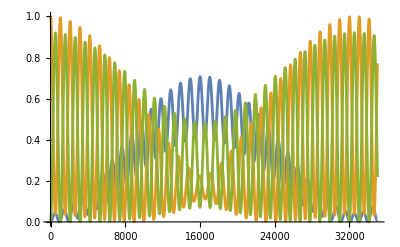

```mathematica
ListPlot[{Pee,Pem,Pet},DataRange->{0,35000},Joined->True]
```

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}.{1,2,3}
```

{a+2 b+3 c,d+2 e+3 f,g+2 h+3 i}

```mathematica
Series[T[z-l],{z,l,2}]
```

T[0]+T'[0] (z-l)+1/2 T''[0] (z-l)^2+O[z-l]^3

```mathematica
Series[T[z+l],{z,l,2}]
```

T[2 l]+T'[2 l] (z-l)+1/2 T''[2 l] (z-l)^2+O[z-l]^3

```mathematica
Series[v[y],{y,0,2}]
```

v[0]+v'[0] y+1/2 v''[0] y^2+O[y]^3

```mathematica
Series[T[z-l],{z,0,2}]
```

T[-l]+T'[-l] z+1/2 T''[-l] z^2+O[z]^3

```mathematica
D[Cos[x],x]
```

-Sin[x]

```mathematica
Eigenvalues[{{a,b},{c,d}}]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

```mathematica
RU={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
```

```mathematica
RU.{{-1,0},{0,1}}.Transpose[RU]/2
```

{{1/2 (-Cos[θ]^2+Sin[θ]^2),Cos[θ] Sin[θ]},{Cos[θ] Sin[θ],1/2 (Cos[θ]^2-Sin[θ]^2)}}

```mathematica
Simplify[%228]//MatrixForm
```

(-1/2 Cos[2 θ] | Cos[θ] Sin[θ]
Cos[θ] Sin[θ] | 1/2 Cos[2 θ])

```mathematica
Integrate[(1-x),{x,1,0}]
```

-1/2

```mathematica
Integrate[Sin[x],{x,0,Pi}]*2Pi
```

4 π

```mathematica
RU.{{-m1^2/(2e),0},{0,m2^2/(2e)}}.Transpose[RU]
```

{{-(m1^2 Cos[θ]^2)/(2 e)+(m2^2 Sin[θ]^2)/(2 e),(m1^2 Cos[θ] Sin[θ])/(2 e)+(m2^2 Cos[θ] Sin[θ])/(2 e)},{(m1^2 Cos[θ] Sin[θ])/(2 e)+(m2^2 Cos[θ] Sin[θ])/(2 e),(m2^2 Cos[θ]^2)/(2 e)-(m1^2 Sin[θ]^2)/(2 e)}}

```mathematica
Simplify[%250]//MatrixForm
```

((m1^2 Cos[θ]^2-m2^2 Sin[θ]^2)/(2 e) | -((m1^2+m2^2) Sin[2 θ])/(4 e)
-((m1^2+m2^2) Sin[2 θ])/(4 e) | (-m2^2 Cos[θ]^2+m1^2 Sin[θ]^2)/(2 e))

```mathematica
ArcTan[0]
```

0

```mathematica
?If
```

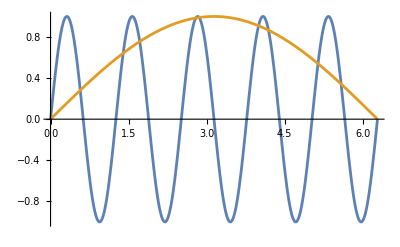

```mathematica
Plot[{Sin[5x],Sin[0.5x]},{x,0,2Pi}]
```

```mathematica
sol=NDSolve[{I ve'[t]==1/(4*10^6)10.2*10^-5 (-0.372827037646145 ve[t]+0.9279008567729636 vm[t])+(5*10^-3Cos[-t/10^10/5]ve[t])/(4*10^6),I vm'[t]==1/(4*10^6)10.2*10^-5(0.9279008567729636 ve[t]+0.372827037646145 vm[t]),ve[0]==1,vm[0]==0},{ve,vm},{t,0,10^12}]
```

{{ve→InterpolatingFunction[…],vm→InterpolatingFunction[…]}}

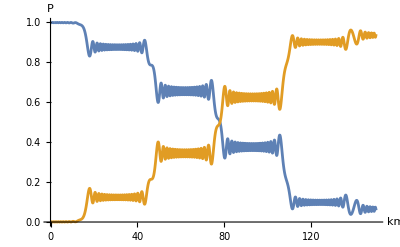

```mathematica
Plot[Evaluate[{ve[t/(1.97*10^-10)]*Conjugate[ve[t/(1.97*10^-10)]],vm[t/(1.97*10^-10)]*Conjugate[vm[t/(1.97*10^-10)]]}/.sol],{t,0,150},PlotRange->{0,1},AxesLabel->{"km",P}]
```

```mathematica
Evaluate[{ve[t]*Conjugate[ve[t]],vm[t]*Conjugate[ve[t]]}/.sol]/.t->10^12
```

{{0.363793+0. ⅈ,-0.255626+0.407558 ⅈ}}

```mathematica
Evaluate[{ve[t]*Conjugate[ve[t]],ve[t]*Conjugate[vm[t]]}/.sol]/.t->10^12
```

{{0.363793+0. ⅈ,-0.255626-0.407558 ⅈ}}

```mathematica
0.156+0.844
```

1.

```mathematica
D[{f[x],y[x]},x]
```

{f'[x],y'[x]}

```mathematica
I D[{ve[t],vm[t]},t]==(1.27*0.759*10^-4)/e{{-Cos[ArcSin[Sqrt[0.861]]],Sin[ArcSin[Sqrt[0.861]]]},{Sin[ArcSin[Sqrt[0.861]]],Cos[ArcSin[Sqrt[0.861]]]}}.{ve[t],vm[t]}
```

{ⅈ ve'[t],ⅈ vm'[t]}=={(0.000096393 (-0.372827 ve[t]+0.927901 vm[t]))/e,(0.000096393 (0.927901 ve[t]+0.372827 vm[t]))/e}

```mathematica
5*10^27*(1.239*10^-4)^3
```

9.51007×10^15

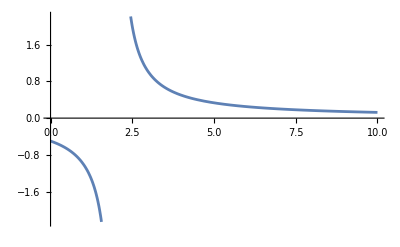

```mathematica
Plot[1/(x-2),{x,0,10}]
```

```mathematica
NIntegrate[1/(x-2),{x,0,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.01156}. NIntegrate obtained -1.06622 and 4.00591 for the integral and error estimates.

-1.06622